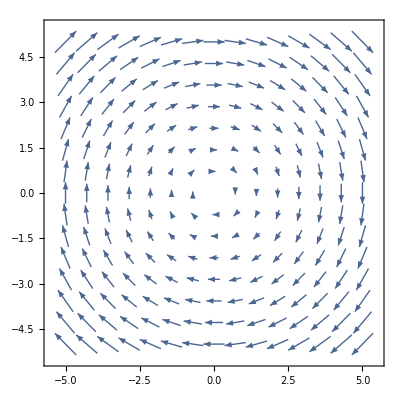

```mathematica
a1=0;
a2=0;
A=1;
B=1;
VectorPlot[{y,0},{x,-5,5},{y,-5,5}];
VectorPlot[{0,-x},{x,-5,5},{y,-5,5}];
VectorPlot[{A(y+a1 x),B(-x+ a2 y)},{x,-5,5},{y,-5,5}]
```

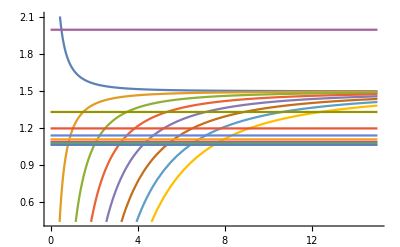

```mathematica
gL[j_,l_]:=1+(j(j+1)-l(l+1)+3/4)/(2j(j+1))
Plot[{gL[j,0],gL[j,1],gL[j,2],gL[j,3],gL[j,4],gL[j,5],gL[j,6],gL[j,7],gL[1/2,0],gL[3/2,1],gL[5/2,2],gL[7/2,3],gL[9/2,4],gL[11/2,5],gL[13/2,6],gL[15/2,7]},{j,0,15}]
```

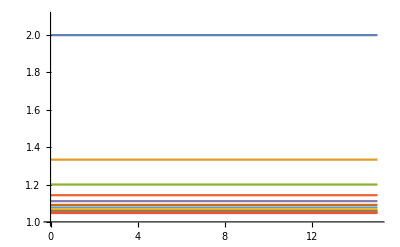

2

```mathematica
gL[j_,l_]:=1+(j(j+1)-l(l+1)+3/4)/(2j(j+1))
tab1=Table[gL[n+1/2,n],{n,0,10}];
Plot[tab1,{j,0,15},PlotRange->{1,2.1}]
```

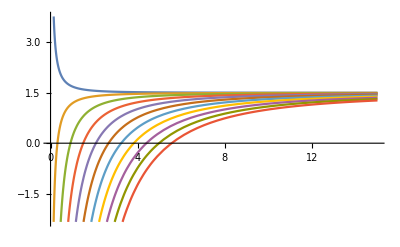

```mathematica
gL[j_,l_]:=1+(j(j+1)-l(l+1)+3/4)/(2j(j+1))
tab2=Table[gL[l+1/2,n],{n,0,10}];
Plot[tab2,{l,0,15}]
```

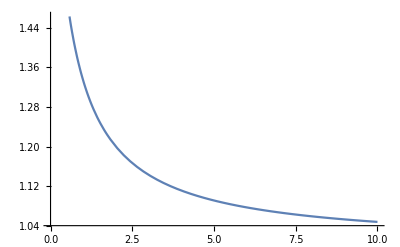

```mathematica
gL[j_,l_]:=1+(j(j+1)-l(l+1)+3/4)/(2j(j+1))
Q=FullSimplify[gL[l+1/2,l]];
Plot[Q,{l,0,10}]
```

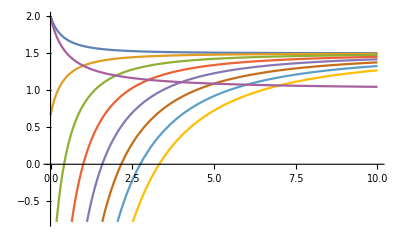

```mathematica
Plot[{gL[l+1/2,0],gL[l+1/2,1],gL[l+1/2,2],gL[l+1/2,3],gL[l+1/2,4],gL[l+1/2,5],gL[l+1/2,6],gL[l+1/2,7],1+1/(1+2 l)},{l,0,10}]
```

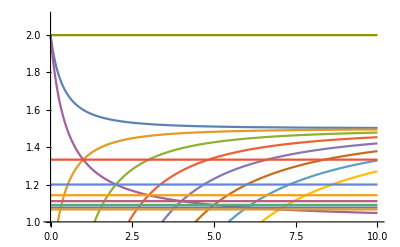

```mathematica
Plot[{gL[l+1/2,0],gL[l+1/2,1],gL[l+1/2,2],gL[l+1/2,3],gL[l+1/2,4],gL[l+1/2,5],gL[l+1/2,6],gL[l+1/2,7],1+1/(1+2 l),gL[1/2,0],gL[3/2,1],gL[5/2,2],gL[7/2,3],gL[9/2,4],gL[11/2,5],gL[13/2,6],gL[15/2,7]},{l,0,10},PlotRange->{1,2.1}]
```

```mathematica
Plot3D[gL[j,l],{j,-5,5},{l,-5,5}]
```

-Graphics3D-

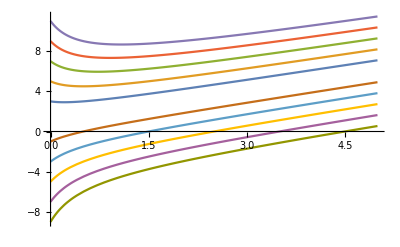

```mathematica
data=Table[gL[l+1/2,l](l+1/2+n),{n,5}];
data2=Table[gL[l+1/2,l](l+1/2-n),{n,5}];
Plot[{data,data2},{l,0,5}]
```

1+1/(1+2 l)

(2 l)/(1+2 l)

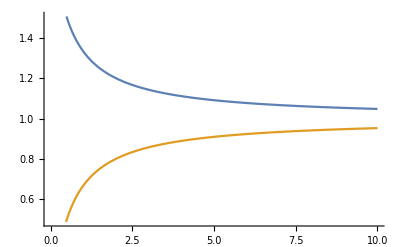

```mathematica
gL[j_,l_]:=1+(j(j+1)-l(l+1)+3/4)/(2j(j+1))
Q1=FullSimplify[gL[l+1/2,l]]
Q2=FullSimplify[gL[l-1/2,l]]
Plot[{Q1,Q2},{l,0,10}]
```

```mathematica
FullSimplify[1+1/(1+2 l)==(2+2l)/(1+2l)]
```

True

```mathematica
gLPos[l_,k_]:=(l+1/2-k)(2+2l)/(1+2l)
gLNeg[l_,k_]:=(l-1/2-k)(2l)/(1+2l)
DataPos=Table[gLPos[l,k],{k,0,2l+1}];
DataNeg=Table[gLNeg[l,k],{k,0,2l-1}];
DiscretePlot[{DataPos,DataNeg},{l,0,5}]
```

Table::iterb: Iterator {k, 0, 1 + 2\ l} does not have appropriate bounds.

Table::iterb: Iterator {k, 0, -1 + 2\ l} does not have appropriate bounds.

Map::level: Level specification {System`DiscretePlotDump`n} is not of the form n, {n}, or {m, n}.

Transpose::tperm: Permutation {2, 1} is longer than the dimensions {2} of the expression.

Map::level: Level specification Transpose[{{{0}, {1}, {2}, {3}, {4}, {5}}, {System`DiscretePlotDump`n}}, {2, 1}] is not of the form n, {n}, or {m, n}.

General::stop: Further output of Map :: level will be suppressed during this calculation.

Transpose::tperm: Permutation {2, 1} is longer than the dimensions {2} of the expression.

General::stop: Further output of Transpose :: tperm will be suppressed during this calculation.

Transpose::list: List expected at position 2 in Transpose[True, True].

MapThread::mptd: Object Map[Transpose[True, True], {True, True, True, True, True, True}, Transpose[True, True]] at position {2, 1} in MapThread[And, {Map[Transpose[True, True], {True, True, True, True, True, True}, Transpose[True, True]], Map[Charting`realNumericQ[If[SameQ[« 2 »] && Unequal[« 2 »], Table[Indeterminate, {« 1 »}], N[Slot[« 1 »], System`DiscretePlotDump`modelData$45504[« 1 »]]]] &, {False, False, False, False, False, False}, {False}]}, 2] has only 0 of required 2 dimensions.

General::stop: Further output of MapThread :: mptd will be suppressed during this calculation.

Transpose::list: List expected at position 2 in Transpose[True, True].

General::stop: Further output of Transpose :: list will be suppressed during this calculation.

Pick::incomp: Expressions {Map[If[Head[Slot[« 1 »]] === List && Length[Slot[« 1 »]] ≠ System`DiscretePlotDump`max, Table[Indeterminate, {System`DiscretePlotDump`max}], N[#1, System`DiscretePlotDump`modelData$45504["WorkingPrecision"]]] &, {{1., -1.}, {2., « 2 », -2.}, {« 1 »}, « 1 », {5., « 8 », -5.}, {6., 4.90909, 3.81818, 2.72727, 1.63636, 0.545455, -0.545455, -1.63636, -2.72727, -3.81818, -4.90909, -6.}}, {System`DiscretePlotDump`n}], « 1 »} and {Map[Charting`realNumericQ[If[Head[« 1 »] === List && Length[« 1 »] ≠ System`DiscretePlotDump`max, Table[Indeterminate, {System`DiscretePlotDump`max}], N[#1, System`DiscretePlotDump`modelData$45504["WorkingPrecision"]]]] &, {False, False, False, False, False, False}, {False}], Map[Charting`realNumericQ[If[Head[« 1 »] === List && Length[« 1 »] ≠ System`DiscretePlotDump`max, Table[Indeterminate, {System`DiscretePlotDump`max}], N[#1, System`DiscretePlotDump`modelData$45504["WorkingPrecision"]]]] &, {False, « 4 », False}, {False}]} have incompatible shapes.

General::stop: Further output of Pick :: incomp will be suppressed during this calculation.

Set::shape: Lists {System`DiscretePlotDump`low, System`DiscretePlotDump`high} and System`DiscretePlotDump`quantile[Pick[Map[Transpose[{0., 1., 2., 3., 4., 5., If[And[« 2 »], Table[« 2 »], N[« 2 »]] &}, {2, 1}], « 1 », Transpose[{0., 1., 2., 3., 4., 5., System`DiscretePlotDump`n}, {2, 1}]], MapThread[And, {Map[Transpose[True, True], {True, True, True, True, True, True}, Transpose[True, True]], Map[Charting`realNumericQ[If[« 3 »]] &, {False, False, False, False, False, False}, {False}]}, 2]], {0.175, 0.825}] are not the same shape.

Transpose::nmtx: The first two levels of {} cannot be transposed.

Transpose::nmtx: The first two levels of {Transpose[{}], Transpose[{}]} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[And, {{Map[Transpose[True, True], {True, True, True, True, True, True}, Transpose[True, True]], Map[Charting`realNumericQ[If[And[« 2 »], Table[« 2 »], N[« 2 »]]] &, {False, False, False, False, False, False}, {False}]}, {True, True, True, True, True, True}}]; dimensions are 2 and 6.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[And, {{Map[Transpose[True, True], {True, True, True, True, True, True}, Transpose[True, True]], Map[Charting`realNumericQ[If[And[« 2 »], Table[« 2 »], N[« 2 »]]] &, {False, False, False, False, False, False}, {False}]}, {False, False, False, False, False, False}}]; dimensions are 2 and 6.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[And, {{Map[Transpose[True, True], {True, True, True, True, True, True}, Transpose[True, True]], Map[Charting`realNumericQ[If[And[« 2 »], Table[« 2 »], N[« 2 »]]] &, {False, False, False, False, False, False}, {False}]}, {True, True, True, True, True, True}}]; dimensions are 2 and 6.

General::stop: Further output of MapThread :: mptc will be suppressed during this calculation.

Split::normal: Nonatomic expression expected at position 1 in Split[And].

Split::normal: Nonatomic expression expected at position 1 in Split[0].

First::normal: Nonatomic expression expected at position 1 in First[And].

Split::normal: Nonatomic expression expected at position 1 in Split[2].

General::stop: Further output of Split :: normal will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[2].

General::stop: Further output of First :: normal will be suppressed during this calculation.

-Graphics-

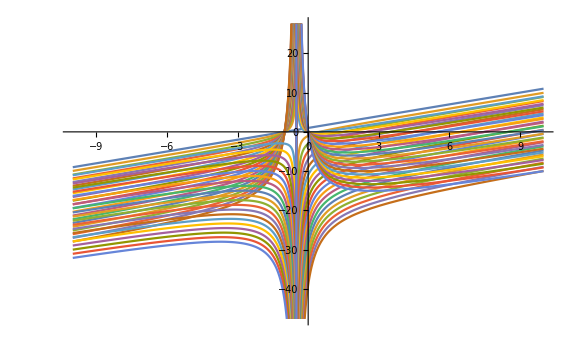

```mathematica
Show[%10,ImageSize->Large]
```

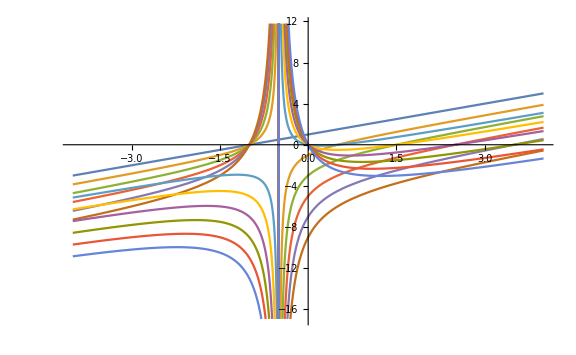

```mathematica
Show[%397,ImageSize->Large]
```

```mathematica
gLPos[1,0]
gLPos[1,1]
gLPos[1,2]
gLPos[1,3]
```

2

2/3

-2/3

-2